```mathematica
Quit[];
```

```mathematica
(**************************************************************)
(* 农田土壤水量平衡统计学模型 (AIM-AS) *)

(* 在 Rodriguez-Iturbe(1999), Laio(2001), Vervoort (2008), Vico(2011)
等人的基础上耦合灌溉参数与潜水埋深，建立了稳定条件下土壤饱和度概率
密度函数解析式以及农田水量计算公式. *)
(* 作者: 黄仲冬 *)
(* 机构: 中国农业科学院农田灌溉研究所 *)
(* 邮箱: zdhuang@126.com *)

(* 输入参数说明 *)
(* α    - 日降雨事件的平均雨量, mm *)
(* λ    - 日降雨事件的发生频率, d^-1 *)
(* Emax - 日潜在蒸发蒸腾量, mm/d *)
(* Zr   - 作物主要根系吸水层深度或计划湿润层深度, mm *)
(* n    - 土壤孔隙度 *)
(* sr   - 残余饱和度或凋萎饱和度 *)
(* sa   - 作物开始产生水分胁迫的土壤饱和度 *)
(* sf   - 田持饱和度 *)
(* Ks   - 土壤饱和导水率, mm/d *)
(* b    - 土壤水分特征曲线参数 *)
(* hb   - 土壤进气值, mm *)
(* Zg   - 地下水埋深, mm *)
(* si   - 灌水下限 *)
(* st   - 灌水上限 *)
(* 其余为中间变量 *)

(* 函数说明 *)
(* RAPDF[s]  - 无灌溉农田土壤饱和度概率密度函数, 无潜水位 *)
(* RAGPDF[s] - 无灌溉农田土壤饱和度概率密度函数, 有潜水位 *)
(* DIPDF[s]  - 亏缺灌溉农田土壤饱和度概率密度函数, 无潜水位 *)
(* DIGPDF[s] - 亏缺灌溉农田土壤饱和度概率密度函数, 有潜水位 *)
(* SIPDF[s]  - 充分灌溉农田土壤饱和度概率密度函数, 无潜水位 *)
(* SIGPDF[s] - 充分灌溉农田土壤饱和度概率密度函数, 有潜水位 *)
(**************************************************************)

(* 中间变量 *)
η=Emax/(n Zr);
γ=(n Zr)/α;
β=2 b+4;
m=Ks/(n Zr (ⅇ^(β(1-sf))-1));
m0=Ks/(n Zr (ⅇ^(β(1-se))-1));
m2=(Ks/(n Zr ))((5b+6)/(2b+6))(hb/(Zg-Zr))^(2+3/b);
m1=m2/(1-ⅇ^(β (sa-se)));
se=Min[Max[(hb/(Zg-Zr))^(1/b),sf],1.0];
sc=Min[(m2/η )(sa-sr)+sr,1.0];

(**************************************************************)
(* 无灌溉农田土壤饱和度概率密度函数 *)
(* RAPDF  - 无潜水位 *)
(* RAGPDF - 有潜水位 *)
(**************************************************************)
RAPDF[s_]:=Piecewise[{
{(ⅇ^(-s γ+((-sa+sr) λ Log[(sa-sr)/(s-sr)])/η) (sa-sr))/((s-sr) η),sr<s<sa},
{ⅇ^(-s γ+((s-sa) λ)/η)/η,sa≤s≤sf},
{ⅇ^(-s γ+((-sa+sf) λ)/η+(λ ((-s+sf) β-Log[η]+Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η)))/((-1+ⅇ^((s-sf) β)) m+η),sf<s≤1}
}];
RAGPDF[s_]:=Piecewise[{
{Piecewise[{
{(ⅇ^(-s γ+((sa-sc) λ Log[(sa-sc)/(s-sc)])/(m2-η)) (sa-sc))/((s-sc) (-m2+η)),sc<s<sa},
{ⅇ^(-s γ+(λ ((-s+sa) β+Log[(-1+ⅇ^((s-se) β)) m1+η]-Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η)))/(-(1-ⅇ^((s-se) β)) m1+η),sa≤s≤se},
{ⅇ^(-s γ+(λ ((-s+se) β-Log[η]+Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))+(λ ((sa-se) β+Log[η]-Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η)))/((-1+ⅇ^((s-se) β)) m0+η),se<s≤1}
}],m1<η},
{Piecewise[{
{ⅇ^(-(s-se) β-s γ-((-1+ⅇ^((-s+se) β)) λ)/(β η))/η,sa<s≤se},
{ⅇ^(-s γ+(λ ((-s+se) β-Log[η]+Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η)))/((-1+ⅇ^((s-se) β)) m0+η),se<s≤1}
}],m1≥η}
}];

(**************************************************************)
(* 亏缺灌溉农田土壤饱和度概率密度函数 *)
(* DIPDF  - 无潜水位 *)
(* DIGPDF - 有潜水位 *)
(**************************************************************)
DIPDF[s_]:=Piecewise[{
{(1/((s-sr) η))ⅇ^(-(s-si) γ-((sa-sr) λ Log[(si-sr)/(s-sr)])/η) (sa-sr) (1-ⅇ^((-si+st) γ) ((-si+sr)/(sr-st))^(((sa-sr) λ)/η) HeavisideTheta[s-st]-ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ]-Gamma[(η-sa λ+sr λ)/η,(sr-st) γ]+(-Gamma[(η-sa λ+sr λ)/η,(-s+sr) γ]+Gamma[(η-sa λ+sr λ)/η,(sr-st) γ]) HeavisideTheta[-s+st])),si≤s<sa},
{Piecewise[{
{(1/η)ⅇ^(-(sa-si) γ-(s-sa) (γ-λ/η)-((sa-sr) λ Log[(si-sr)/(sa-sr)])/η) (1-ⅇ^((-si+st) γ) ((-si+sr)/(sr-st))^(((sa-sr) λ)/η)+ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (-Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ]+Gamma[(η-sa λ+sr λ)/η,(sr-st) γ])),st<sa},
{(1/η)ⅇ^(-(sa-si) γ-(s-sa) (γ-λ/η)-((sa-sr) λ Log[(si-sr)/(sa-sr)])/η) (1+ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (Gamma[(η-sa λ+sr λ)/η,(-sa+sr) γ]-Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ])-(1/(γ η-λ))ⅇ^(-si γ-((s+st) λ)/η) ((si-sr)/(sa-sr))^(((sa-sr) λ)/η) (ⅇ^(st γ+((s+sa) λ)/η) (γ η-λ) HeavisideTheta[s-st]+γ η (-ⅇ^(st γ+((s+sa) λ)/η)+ⅇ^(sa γ+((s+st) λ)/η)+(ⅇ^(st γ+((s+sa) λ)/η)-ⅇ^(s γ+((sa+st) λ)/η)) HeavisideTheta[-s+st]))),st≥sa}
}],sa≤s≤sf},
{Piecewise[{
{(1/((-1+ⅇ^((s-sf) β)) m+η))ⅇ^(-s γ+sf γ-(sa-si) γ-(-sa+sf) (γ-λ/η)-((sa-sr) λ Log[(si-sr)/(sa-sr)])/η-(λ ((s-sf) β+Log[η]-Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η))) (1-ⅇ^((-si+st) γ) ((-si+sr)/(sr-st))^(((sa-sr) λ)/η)+ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (-Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ]+Gamma[(η-sa λ+sr λ)/η,(sr-st) γ])),st<sa},
{(1/((-1+ⅇ^((s-sf) β)) m+η))ⅇ^(-s γ+sf γ-(sa-si) γ-(-sa+sf) (γ-λ/η)-((sa-sr) λ Log[(si-sr)/(sa-sr)])/η-(λ ((s-sf) β+Log[η]-Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η))) (1+(ⅇ^(-si γ-(st λ)/η) ((si-sr)/(sa-sr))^(((sa-sr) λ)/η) (-ⅇ^(sa γ+(st λ)/η) γ η+ⅇ^(st γ+(sa λ)/η) λ))/(γ η-λ)+ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (Gamma[(η-sa λ+sr λ)/η,(-sa+sr) γ]-Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ])),sa≤st≤sf},
{(1/((-1+ⅇ^((s-sf) β)) m+η))ⅇ^(-s γ+sf γ-(sa-si) γ-(-sa+sf) (γ-λ/η)-((sa-sr) λ Log[(si-sr)/(sa-sr)])/η-(λ ((s-sf) β+Log[η]-Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η))) (1-(ⅇ^(-si γ) (ⅇ^(sa γ)-ⅇ^((sf γ η+sa λ-sf λ)/η)) ((si-sr)/(sa-sr))^(((sa-sr) λ)/η) γ η)/(γ η-λ)+ⅇ^((-si+sr) γ) ((-si+sr) γ)^(((sa-sr) λ)/η) (Gamma[(η-sa λ+sr λ)/η,(-sa+sr) γ]-Gamma[(η-sa λ+sr λ)/η,(-si+sr) γ])-ⅇ^((m (-si γ η+st γ η+sa λ-sf λ)+η (si γ η-st γ η-sa λ+st λ))/((m-η) η)) ((si-sr)/(sa-sr))^(((sa-sr) λ)/η) η^(λ/(m β-β η)) ((-1+ⅇ^((-sf+st) β)) m+η)^(-λ/(m β-β η)) HeavisideTheta[s-st]+((si-sr)/(sa-sr))^(((sa-sr) λ)/η) γ ((1/(m γ-γ η+λ))ⅇ^(-(m si γ η+m (-sa+sf) λ+η (-si γ η+sa λ))/((m-η) η)) (m-η) ((-1+ⅇ^((s-sf) β)) m+η)^(-λ/(m β-β η)) HeavisideTheta[-s+st] (-ⅇ^((sf (m γ-γ η+λ))/(m-η)) (-(η/(m-η)))^(λ/(m β-β η)) ((-1+ⅇ^((s-sf) β)) m+η)^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),m/(m-η)]+ⅇ^((s (m γ-γ η+λ))/(m-η)) (1-(ⅇ^((s-sf) β) m)/(m-η))^(λ/(m β-β η)) η^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),(ⅇ^((s-sf) β) m)/(m-η)])+(1/(m γ-γ η+λ))ⅇ^(-(m si γ η+m (-sa+sf) λ+η (-si γ η+sa λ))/((m-η) η)) (m-η) ((-1+ⅇ^((-sf+st) β)) m+η)^(-λ/(m β-β η)) (1-HeavisideTheta[-s+st]) (ⅇ^((st (m γ-γ η+λ))/(m-η)) (1-(ⅇ^((-sf+st) β) m)/(m-η))^(λ/(m β-β η)) η^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),(ⅇ^((-sf+st) β) m)/(m-η)]-ⅇ^((sf (m γ-γ η+λ))/(m-η)) (-(η/(m-η)))^(λ/(m β-β η)) ((-1+ⅇ^((-sf+st) β)) m+η)^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m (β+γ)-β η-γ η+λ)/(m β-β η),m/(m-η)]))),sf<st≤1}
}],sf<s≤1}
}];
DIGPDF[s_]:=Piecewise[{
{Piecewise[{
{Piecewise[{
{(1/((s-sc) (-m2+η)))ⅇ^(-(s-si) γ-((-sa+sc) λ Log[(-sc+si)/(s-sc)])/(m2-η)) (sa-sc) (1-ⅇ^((-si+st) γ) ((sc-si)/(sc-st))^(((-sa+sc) λ)/(m2-η)) HeavisideTheta[s-st]-ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ]-Gamma[1+((sa-sc) λ)/(m2-η),(sc-st) γ]+(-Gamma[1+((sa-sc) λ)/(m2-η),(-s+sc) γ]+Gamma[1+((sa-sc) λ)/(m2-η),(sc-st) γ]) HeavisideTheta[-s+st])),si≤s<sa},
{Piecewise[{
{(1/(-(1-ⅇ^((s-se) β)) m1+η))ⅇ^(-s γ+sa γ-(sa-si) γ-((-sa+sc) λ Log[(-sc+si)/(sa-sc)])/(m2-η)-(λ ((s-sa) β-Log[(-1+ⅇ^((s-se) β)) m1+η]+Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η))) (1-ⅇ^((-si+st) γ) ((sc-si)/(sc-st))^(((-sa+sc) λ)/(m2-η))+ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (-Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ]+Gamma[1+((sa-sc) λ)/(m2-η),(sc-st) γ])),st<sa},
{(1/(-(1-ⅇ^((s-se) β)) m1+η))ⅇ^(-s γ+sa γ-(sa-si) γ-((-sa+sc) λ Log[(-sc+si)/(sa-sc)])/(m2-η)-(λ ((s-sa) β-Log[(-1+ⅇ^((s-se) β)) m1+η]+Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η))) (1+ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (Gamma[1+((sa-sc) λ)/(m2-η),(-sa+sc) γ]-Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ])-ⅇ^(-si γ+st γ+((-sa+st) λ)/(m1-η)) ((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) HeavisideTheta[s-st]+((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) γ ((1/(m1 γ-γ η+λ))ⅇ^(-si γ-(sa λ)/(m1-η)) (m1-η) ((-1+ⅇ^((s-se) β)) m1+η)^(-λ/(m1 β-β η)) HeavisideTheta[-s+st] (ⅇ^((s (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((s-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((s-se) β) m1)/(m1-η)]-ⅇ^((sa (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((sa-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((s-se) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((sa-se) β) m1)/(m1-η)])+(1/(m1 γ-γ η+λ))ⅇ^(-si γ-(sa λ)/(m1-η)) (m1-η) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) (1-HeavisideTheta[-s+st]) (-ⅇ^((sa (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((sa-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((sa-se) β) m1)/(m1-η)]+ⅇ^((st (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((-se+st) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+st) β) m1)/(m1-η)]))),st≥ sa}
}],sa≤s≤se},
{Piecewise[{
{(1/((-1+ⅇ^((s-se) β)) m0+η))ⅇ^(-s γ+sa γ-(sa-si) γ-((-sa+sc) λ Log[(-sc+si)/(sa-sc)])/(m2-η)-(λ ((s-se) β+Log[η]-Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))+(λ ((sa-se) β+Log[η]-Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η))) (1-ⅇ^((-si+st) γ) ((sc-si)/(sc-st))^(((-sa+sc) λ)/(m2-η))+ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (-Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ]+Gamma[1+((sa-sc) λ)/(m2-η),(sc-st) γ])),st<sa},
{(1/((-1+ⅇ^((s-se) β)) m0+η))ⅇ^(-s γ+sa γ-(sa-si) γ-((-sa+sc) λ Log[(-sc+si)/(sa-sc)])/(m2-η)-(λ ((s-se) β+Log[η]-Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))+(λ ((sa-se) β+Log[η]-Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η))) (1-ⅇ^((m1 (-si+st) γ+si γ η-st γ η-sa λ+st λ)/(m1-η)) ((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η))+ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (Gamma[1+((sa-sc) λ)/(m2-η),(-sa+sc) γ]-Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ])+(1/(m1 γ-γ η+λ))ⅇ^(-si γ-(sa λ)/(m1-η)) ((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) γ (m1-η) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) (-ⅇ^((sa (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((sa-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((sa-se) β) m1)/(m1-η)]+ⅇ^((st (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((-se+st) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+st) β) m1)/(m1-η)])),sa≤st≤se},
{(1/((-1+ⅇ^((s-se) β)) m0+η))ⅇ^(-s γ+sa γ-(sa-si) γ-((-sa+sc) λ Log[(-sc+si)/(sa-sc)])/(m2-η)-(λ ((s-se) β+Log[η]-Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))+(λ ((sa-se) β+Log[η]-Log[(-1+ⅇ^((sa-se) β)) m1+η]))/(β (m1-η))) (1+ⅇ^((sc-si) γ) ((sc-si) γ)^(((-sa+sc) λ)/(m2-η)) (Gamma[1+((sa-sc) λ)/(m2-η),(-sa+sc) γ]-Gamma[1+((sa-sc) λ)/(m2-η),(sc-si) γ])-ⅇ^((m0 (m1 (si-st) γ-si γ η+st γ η+sa λ-se λ)+m1 (-si γ η+st γ η+se λ-st λ)+η (si γ η-st γ η-sa λ+st λ))/((m0-η) (-m1+η))) ((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) η^(((m0-m1) λ)/(β (m0-η) (-m1+η))) ((-1+ⅇ^((-se+st) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) HeavisideTheta[s-st]+((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) γ ((1/(-m0 γ+γ η-λ))ⅇ^(-si γ+(m0 sa λ)/((m1-η) (-m0+η))-(m0 se λ)/((m1-η) (-m0+η))+(m1 se λ)/((m1-η) (-m0+η))-(sa η λ)/((m1-η) (-m0+η))) η^(-λ/(m1 β-β η)) (-m0+η) ((-1+ⅇ^((s-se) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) HeavisideTheta[-s+st] (ⅇ^((s (m0 γ-γ η+λ))/(m0-η)) (1-(ⅇ^((s-se) β) m0)/(m0-η))^(λ/(m0 β-β η)) η^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 β+m0 γ-β η-γ η+λ)/(m0 β-β η),(ⅇ^((s-se) β) m0)/(m0-η)]-ⅇ^((se (m0 γ-γ η+λ))/(m0-η)) (-(η/(m0-η)))^(λ/(m0 β-β η)) ((-1+ⅇ^((s-se) β)) m0+η)^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 (β+γ)-β η-γ η+λ)/(m0 β-β η),m0/(m0-η)])+(1/(-m0 γ+γ η-λ))ⅇ^(-si γ+(m0 sa λ)/((m1-η) (-m0+η))-(m0 se λ)/((m1-η) (-m0+η))+(m1 se λ)/((m1-η) (-m0+η))-(sa η λ)/((m1-η) (-m0+η))) η^(-λ/(m1 β-β η)) (-m0+η) ((-1+ⅇ^((-se+st) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) (1-HeavisideTheta[-s+st]) (ⅇ^((st (m0 γ-γ η+λ))/(m0-η)) (1-(ⅇ^((-se+st) β) m0)/(m0-η))^(λ/(m0 β-β η)) η^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 β+m0 γ-β η-γ η+λ)/(m0 β-β η),(ⅇ^((-se+st) β) m0)/(m0-η)]-ⅇ^((se (m0 γ-γ η+λ))/(m0-η)) (-(η/(m0-η)))^(λ/(m0 β-β η)) ((-1+ⅇ^((-se+st) β)) m0+η)^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 (β+γ)-β η-γ η+λ)/(m0 β-β η),m0/(m0-η)]))-(1/(m1 γ-γ η+λ))ⅇ^(-si γ-(sa λ)/(m1-η)) ((-sc+si)/(sa-sc))^(((-sa+sc) λ)/(m2-η)) γ (m1-η) η^(-λ/(m1 β-β η)) (-ⅇ^((se (m1 γ-γ η+λ))/(m1-η)) (-(η/(m1-η)))^(λ/(m1 β-β η)) ((-1+ⅇ^((sa-se) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),m1/(m1-η)]+ⅇ^((sa (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((sa-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) η^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((sa-se) β) m1)/(m1-η)])),se<st≤1}
}],se<s≤1}}],m1<η},
{Piecewise[{
{ⅇ^(-(s-se) β-s γ-((-1+ⅇ^((-s+se) β)) λ)/(β η))/η,sa<s≤se},
{ⅇ^(-s γ+(λ ((-s+se) β-Log[η]+Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η)))/((-1+ⅇ^((s-se) β)) m0+η),se<s≤1}
}],m1≥η}
}],si>sc},
{RAGPDF[s],si≤sc}
}];

(**************************************************************)
(* 充分灌溉农田土壤饱和度概率密度函数 *)
(* SIPDF  - 无潜水位 *)
(* SIGPDF - 有潜水位 *)
(**************************************************************)
SIPDF[s_]:=Piecewise[{
{(1/η)ⅇ^(-(s-si) (γ-λ/η)) (1+(1/(γ η-λ))ⅇ^(-((si-st) (γ η-λ))/η) ((-γ η+λ) HeavisideTheta[s-st]-γ η (-1+ⅇ^(((si-st) (γ η-λ))/η)-(-1+ⅇ^(((s-st) (γ η-λ))/η)) HeavisideTheta[-s+st]))),si≤s≤sf},
{Piecewise[{
{(ⅇ^(-s γ+sf γ-(sf-si) (γ-λ/η)-(λ ((s-sf) β+Log[η]-Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η))) (1+(-γ η+ⅇ^(-((si-st) (γ η-λ))/η) λ)/(γ η-λ)))/((-1+ⅇ^((s-sf) β)) m+η),st≤sf},
{(1/((-1+ⅇ^((s-sf) β)) m+η))ⅇ^(-s γ+sf γ-(sf-si) (γ-λ/η)-(λ ((s-sf) β+Log[η]-Log[(-1+ⅇ^((s-sf) β)) m+η]))/(β (m-η))) (1+((-1+ⅇ^(((sf-si) (γ η-λ))/η)) γ η)/(γ η-λ)-ⅇ^(st γ+((-m sf+st η) λ)/((m-η) η)+si (-γ+λ/η)) η^(λ/(m β-β η)) ((-1+ⅇ^((-sf+st) β)) m+η)^(-λ/(m β-β η)) HeavisideTheta[s-st]+(1/(m γ-γ η+λ))ⅇ^((si η (γ η-λ)-m (si γ η+sf λ-si λ))/((m-η) η)) γ (m-η) (HeavisideTheta[-s+st] (-ⅇ^((sf (m γ-γ η+λ))/(m-η)) (-(η/(m-η)))^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),m/(m-η)]+ⅇ^((s (m γ-γ η+λ))/(m-η)) (1-(ⅇ^((s-sf) β) m)/(m-η))^(λ/(m β-β η)) η^(λ/(m β-β η)) ((-1+ⅇ^((s-sf) β)) m+η)^(-λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),(ⅇ^((s-sf) β) m)/(m-η)])+((-1+ⅇ^((-sf+st) β)) m+η)^(-λ/(m β-β η)) (-1+HeavisideTheta[-s+st]) (ⅇ^((sf (m γ-γ η+λ))/(m-η)) (-(η/(m-η)))^(λ/(m β-β η)) ((-1+ⅇ^((-sf+st) β)) m+η)^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),m/(m-η)]-ⅇ^((st (m γ-γ η+λ))/(m-η)) (1-(ⅇ^((-sf+st) β) m)/(m-η))^(λ/(m β-β η)) η^(λ/(m β-β η)) Hypergeometric2F1[λ/(m β-β η),(m γ-γ η+λ)/(m β-β η),(m β+m γ-β η-γ η+λ)/(m β-β η),(ⅇ^((-sf+st) β) m)/(m-η)]))),st>sf}
}],sf<s≤1}
}];
SIGPDF[s_]:=Piecewise[{
{Piecewise[{
{Piecewise[{
{(1/(-(1-ⅇ^((s-se) β)) m1+η))ⅇ^(-s γ+si γ-(λ ((s-si) β-Log[(-1+ⅇ^((s-se) β)) m1+η]+Log[(-1+ⅇ^((-se+si) β)) m1+η]))/(β (m1-η))) (1-ⅇ^(-((si-st) (m1 γ-γ η+λ))/(m1-η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) HeavisideTheta[s-st]+(1/(m1 γ-γ η+λ))ⅇ^(-(si (m1 γ-γ η+λ))/(m1-η)) γ (m1-η) (-ⅇ^((si (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((-se+si) β) m1)/(m1-η))^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+si) β) m1)/(m1-η)]+ⅇ^((st (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((-se+st) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+st) β) m1)/(m1-η)]+((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) HeavisideTheta[-s+st] (ⅇ^((s (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((s-se) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((s-se) β)) m1+η)^(-λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((s-se) β) m1)/(m1-η)]-ⅇ^((st (m1 γ-γ η+λ))/(m1-η)) (1-(ⅇ^((-se+st) β) m1)/(m1-η))^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+st) β) m1)/(m1-η)]))),si≤s≤se},
{Piecewise[{
{(1/((-1+ⅇ^((s-se) β)) m0+η))ⅇ^(-s γ+si γ-(λ ((s-se) β+Log[η]-Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))-(λ ((se-si) β-Log[η]+Log[(-1+ⅇ^((-se+si) β)) m1+η]))/(β (m1-η))) (1+(1/(m1 γ-γ η+λ))(-γ (1-(ⅇ^((-se+si) β) m1)/(m1-η))^(λ/(m1 β-β η)) (m1-η) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+si) β) m1)/(m1-η)]+ⅇ^(-((si-st) (m1 γ-γ η+λ))/(m1-η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+st) β)) m1+η)^(-λ/(m1 β-β η)) (-m1 γ+γ η-λ+γ (1-(ⅇ^((-se+st) β) m1)/(m1-η))^(λ/(m1 β-β η)) (m1-η) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+st) β) m1)/(m1-η)]))),st≤se},
{(1/((-1+ⅇ^((s-se) β)) m0+η))ⅇ^(-s γ+si γ-(λ ((s-se) β+Log[η]-Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η))-(λ ((se-si) β-Log[η]+Log[(-1+ⅇ^((-se+si) β)) m1+η]))/(β (m1-η))) (1-ⅇ^(se (1/(m1-η)+1/(-m0+η)) λ+st (γ+λ/(m0-η))+si (-γ-λ/(m1-η))) η^(((m0-m1) λ)/(β (m0-η) (-m1+η))) ((-1+ⅇ^((-se+st) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) HeavisideTheta[s-st]+γ ((1/(m0 γ-γ η+λ))ⅇ^(-si γ+(se λ)/(m1-η)-(si λ)/(m1-η)+(se λ)/(-m0+η)) η^(-λ/(m1 β-β η)) (-m0+η) ((-1+ⅇ^((-se+st) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) (1-HeavisideTheta[-s+st]) (ⅇ^((se (m0 γ-γ η+λ))/(m0-η)) (-(η/(m0-η)))^(λ/(m0 β-β η)) ((-1+ⅇ^((-se+st) β)) m0+η)^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 β+m0 γ-β η-γ η+λ)/(m0 β-β η),m0/(m0-η)]-ⅇ^((st (m0 γ-γ η+λ))/(m0-η)) (1-(ⅇ^((-se+st) β) m0)/(m0-η))^(λ/(m0 β-β η)) η^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 β+m0 γ-β η-γ η+λ)/(m0 β-β η),(ⅇ^((-se+st) β) m0)/(m0-η)])-(1/(m0 γ-γ η+λ))ⅇ^(-si γ+(se λ)/(m1-η)-(si λ)/(m1-η)+(se λ)/(-m0+η)) η^(-λ/(m1 β-β η)) (-m0+η) ((-1+ⅇ^((s-se) β)) m0+η)^(-λ/(m0 β-β η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) HeavisideTheta[-s+st] (ⅇ^((s (m0 γ-γ η+λ))/(m0-η)) (1-(ⅇ^((s-se) β) m0)/(m0-η))^(λ/(m0 β-β η)) η^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 β+m0 γ-β η-γ η+λ)/(m0 β-β η),(ⅇ^((s-se) β) m0)/(m0-η)]-ⅇ^((se (m0 γ-γ η+λ))/(m0-η)) (-(η/(m0-η)))^(λ/(m0 β-β η)) ((-1+ⅇ^((s-se) β)) m0+η)^(λ/(m0 β-β η)) Hypergeometric2F1[λ/(m0 β-β η),(m0 γ-γ η+λ)/(m0 β-β η),(m0 (β+γ)-β η-γ η+λ)/(m0 β-β η),m0/(m0-η)]))+(1/(m1 γ-γ η+λ))ⅇ^(-si (γ+λ/(m1-η))) γ (m1-η) η^(-λ/(m1 β-β η)) (ⅇ^((se (m1 γ-γ η+λ))/(m1-η)) (-(η/(m1-η)))^(λ/(m1 β-β η)) ((-1+ⅇ^((-se+si) β)) m1+η)^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),m1/(m1-η)]-ⅇ^(si (γ+λ/(m1-η))) (1-(ⅇ^((-se+si) β) m1)/(m1-η))^(λ/(m1 β-β η)) η^(λ/(m1 β-β η)) Hypergeometric2F1[λ/(m1 β-β η),(m1 γ-γ η+λ)/(m1 β-β η),(m1 β+m1 γ-β η-γ η+λ)/(m1 β-β η),(ⅇ^((-se+si) β) m1)/(m1-η)])),st>se}
}],se<s≤1}
}],m1<η},
{Piecewise[{
{ⅇ^(-(s-se) β-s γ-((-1+ⅇ^((-s+se) β)) λ)/(β η))/η,sa<s≤se},
{ⅇ^(-s γ+(λ ((-s+se) β-Log[η]+Log[(-1+ⅇ^((s-se) β)) m0+η]))/(β (m0-η)))/((-1+ⅇ^((s-se) β)) m0+η),se<s≤1}
}],m1≥η}
}],si>sc},
{RAGPDF[s],si≤sc}
}];

(**************************************************************)
(* 灌溉农田土壤饱和度概率密度函数 *)
(* IRPDF  - 无潜水位 *)
(* IRGPDF - 有潜水位 *)
(**************************************************************)
IRPDF[s_]:=Piecewise[{
{DIPDF[s],si<sa},
{SIPDF[s],si≥sa}
}];
IRGPDF[s_]:=Piecewise[{
{DIGPDF[s],si<sa},
{SIGPDF[s],si≥sa}
}];

(**************************************************************)
(* 农田土壤饱和度概率密度函数 *)
(* SSPDF  - 无潜水位 *)
(* SSGPDF - 有潜水位 *)
(**************************************************************)
SSPDF[s_]:=Piecewise[{
{RAPDF[s],si≤sr},
{DIPDF[s],sr<si<sa},
{SIPDF[s],si≥sa}
}];
SSGPDF[s_]:=Piecewise[{
{RAGPDF[s],si≤sc},
{DIGPDF[s],sc<si<sa},
{SIGPDF[s],si≥sa}
}];

(**************************************************************)
(* 农田土壤水分损失函数 *)
(* LOSS  - 无潜水位 *)
(* GLOSS - 有潜水位 *)
(**************************************************************)
LOSS[s_]:=Piecewise[{
{η((s-sr)/(sa-sr)),sr<s<sa},
{η,sa≤s≤sf},
{η+m(ⅇ^(β(s-sf))-1),sf<s≤1}
}];
GLOSS[s_]:=Piecewise[{
{Piecewise[{
{(η-m2)((s-sc)/(sa-sc)),sc<s<sa},
{η-m1(1-ⅇ^(β(s-se))),sa≤s≤se},
{η+m0(ⅇ^(β(s-se))-1),se<s≤1}
}],m1<η},
{Piecewise[{
{η ⅇ^(β(s-se)),sa<s≤se},
{η+m0(ⅇ^(β(s-se))-1),se<s≤1}
}],m1≥η}
}];

(**************************************************************)
(* 蒸发蒸腾速率 *)
(**************************************************************)
EVT[s_]:=Piecewise[{
{Emax((s-sr)/(sa-sr)),sr<s<sa},
{Emax,sa≤s≤1}
}];

(**************************************************************)
(* 深层渗漏速率 *)
(* LEAK  - 无潜水位 *)
(* GLEAK - 有潜水位 *)
(**************************************************************)
LEAK[s_]:=Piecewise[{
{Ks((ⅇ^(β(s-sf))-1)/(ⅇ^(β(1-sf))-1)),sf<s≤1}
}];
GLEAK[s_]:=Piecewise[{
{Ks((ⅇ^(β(s-se))-1)/(ⅇ^(β(1-se))-1)),se<s≤1}
}];

(**************************************************************)
(* 潜水蒸发强度 *)
(**************************************************************)
CF[s_]:=Piecewise[{
{Ks((5b+6)/(2b+6))(hb/(Zg-Zr))^(2+3/b),sc<s<sa},
{Ks((5b+6)/(2b+6))(hb/(Zg-Zr))^(2+3/b)((1-ⅇ^(β(s-se)))/(1-ⅇ^(β(sa-se)))),sa≤s≤se}
}]
```

```mathematica
(* 农田土壤饱和度概率密度函数计算实例 *)
(* 参数取值 *)
αF=15;
λF=0.15;
EmaxF=4.5;
ZrF=500;
nF=0.42;
srF=0.21;
saF=0.40;
sfF=0.64;
KsF=614;
bF=4.5;
hbF=132;
params = {α:>αF,λ:>λF,Emax:>EmaxF,Zr:>ZrF,n:>nF,sr:>srF,sa:>saF,sf:>sfF,Ks:>KsF,b:>bF,si:>siF,st:>stF,hb:>hbF,Zg:>ZgF};
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {s} = {0.500309} 处的 s 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 22.2836+3.10113×10^-15 ⅈ 和 0.00162289.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {s} = {0.600153} 处的 s 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 15.9386 和 0.00177148.

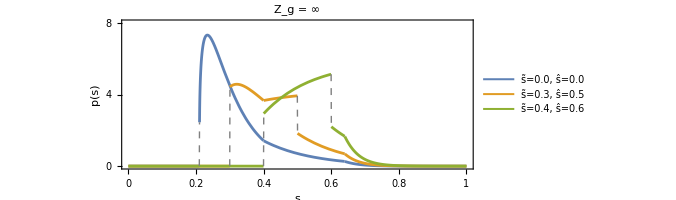

```mathematica
(* Zg = ∞ *)
PDF1[s_]=RAPDF[s]/.params;
C1=1/Chop[NIntegrate[PDF1[s],{s,0,1},Method->"GlobalAdaptive"]];

siF=0.3;stF=0.5;
PDF2[s_]=DIPDF[s]/.params;
C2=1/Chop[NIntegrate[PDF2[s],{s,0,1},Method->"GlobalAdaptive"]];

siF=0.4;stF=0.6;
PDF3[s_]=SIPDF[s]/.params;
C3=1/Chop[NIntegrate[PDF3[s],{s,0,1},Method->"GlobalAdaptive"]];

Plot1=Plot[{C1*PDF1[s],C2*PDF2[s],C3*PDF3[s]},{s,0,1},
PlotRange->{{0,1},{0,8}},
Exclusions->Automatic,
ExclusionsStyle->Directive[Gray,Dashed],
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameTicks->{
{
{{0,"0",{0.01,0}},{2,"2",{0.01,0}},{4,"4",{0.01,0}},{6,"6",{0.01,0}},{8,"8",{0.01,0}},{10,"10",{0.01,0}}},
None
},
{
{{0,"0",{0,0.01}},{0.2,"0.2",{0,0.01}},{0.4,"0.4",{0,0.01}},{0.6,"0.6",{0,0.01}},{0.8,"0.8",{0,0.01}},{1,"1",{0,0.01}}},
{{srF,"s_r",{0.4,0},Directive[Dashed,Gray]},{saF,"s^*",{0.4,0},Directive[Dashed,Gray]},{sfF,"s_f",{0.4,0},Directive[Dashed,Gray]}}
}
},
FrameTicksStyle->Directive[Black,16,FontFamily->"Times"],
FrameLabel->{Style["s",Black,16,FontFamily->"Times"],Style["p(s)",Black,18,FontFamily->"Times"]},
PlotStyle->{Thickness[0.004]},
PlotLabel->Style["Z_g = ∞",16,FontFamily->"Times",Black,Bold],
ImageSize->500,AspectRatio->0.4,
PlotLegends->Placed[LineLegend[{"s̃=0.0, ŝ=0.0","s̃=0.3, ŝ=0.5","s̃=0.4, ŝ=0.6"},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],LegendMarkerSize->{20,5}],{Right,Top}]
]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {s} = {0.500309} 处的 s 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 139.157+1.97578×10^-15 ⅈ 和 0.00501808.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {s} = {0.600153} 处的 s 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 30.5578 和 0.00238289.

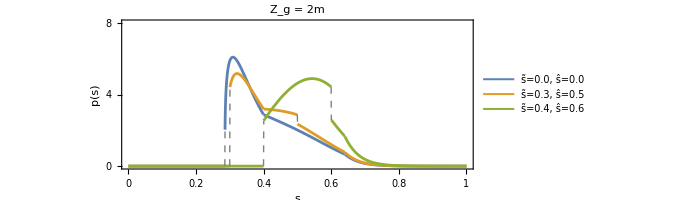

```mathematica
(* Zg = 2m *)
ZgF=2000;

PDF1[s_]=RAGPDF[s]/.params;
C1=1/Chop[NIntegrate[PDF1[s],{s,0,1},Method->"GlobalAdaptive"]];

siF=0.3;stF=0.5;
PDF2[s_]=DIGPDF[s]/.params;
C2=1/Chop[NIntegrate[PDF2[s],{s,0,1},Method->"GlobalAdaptive"]];

siF=0.4;stF=0.6;
PDF3[s_]=SIGPDF[s]/.params;
C3=1/Chop[NIntegrate[PDF3[s],{s,0,1},Method->"GlobalAdaptive"]];

Plot2=Plot[{C1*PDF1[s],C2*PDF2[s],C3*PDF3[s]},{s,0,1},
PlotRange->{{0,1},{0,8}},
Exclusions->Automatic,
ExclusionsStyle->Directive[Gray,Dashed],
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.003]],
FrameTicks->{
{
{{0,"0",{0.01,0}},{2,"2",{0.01,0}},{4,"4",{0.01,0}},{6,"6",{0.01,0}},{8,"8",{0.01,0}},{10,"10",{0.01,0}}},
None
},
{
{{0,"0",{0,0.01}},{0.2,"0.2",{0,0.01}},{0.4,"0.4",{0,0.01}},{0.6,"0.6",{0,0.01}},{0.8,"0.8",{0,0.01}},{1,"1",{0,0.01}}},
{{srF,"s_r",{0.4,0},Directive[Dashed,Gray]},{saF,"s^*",{0.4,0},Directive[Dashed,Gray]},{sfF,"s_f",{0.4,0},Directive[Dashed,Gray]}}
}
},
FrameTicksStyle->Directive[Black,16,FontFamily->"Times"],
FrameLabel->{Style["s",Black,16,FontFamily->"Times"],Style["p(s)",Black,16,FontFamily->"Times"]},
PlotStyle->{Thickness[0.004]},
PlotLabel->Style["Z_g = 2m",16,FontFamily->"Times",Black,Bold],
ImageSize->500,AspectRatio->0.4,
PlotLegends->Placed[LineLegend[{"s̃=0.0, ŝ=0.0","s̃=0.3, ŝ=0.5","s̃=0.4, ŝ=0.6"},LabelStyle->Directive[Black,FontSize->16,FontFamily->"Times"],LegendMarkerSize->{20,5}],{Right,Top}]
]
```